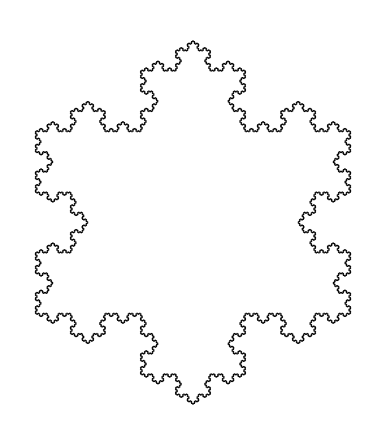

```mathematica
Koch[n_,p1_,p2_]:=If[n==0,
Return[{{p1,p2}}],
Return[Join[
Koch[n-1,p1,p1+(p2-p1)/3],
Koch[n-1,p1+(p2-p1)/3,p1+(p2-p1)/3+{{Cos[60°],-Sin[60°]},{Sin[60°],Cos[60°]}}.(p2-p1)/3],Koch[n-1,p1+(p2-p1)/3+{{Cos[60°],-Sin[60°]},{Sin[60°],Cos[60°]}}.(p2-p1)/3,p2-(p2-p1)/3],
Koch[n-1,p2-(p2-p1)/3,p2]
]
]
]

Snowflake[n_]:=Graphics[Line[Join[Koch[n,{0,0},{1,0}],Koch[n,{1,0},{1/2,-Sqrt[3]/2}],Koch[n,{1/2,-Sqrt[3]/2},{0,0}]]]]

Graphics[Line[Koch[0,{0,0},{1,0}]]];
Snowflake[5]
```

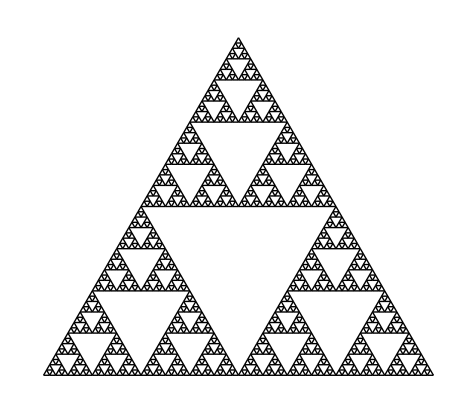

```mathematica
Sierpinski[n_,p1_,p2_,p3_]:=If[n==0,
Return[{{p1,p2},{p2,p3},{p3,p1}}],
Return[Join[
Sierpinski[n-1,p1,(p1+p2)/2,(p1+p3)/2],
Sierpinski[n-1,p2,(p2+p1)/2,(p2+p3)/2],
Sierpinski[n-1,p3,(p3+p1)/2,(p3+p2)/2]
]
]
]

SierpinskiTriangle[n_]:=Graphics[Line[Sierpinski[n,{0,0},{1,0},{1/2,Sqrt[3]/2}]]]

SierpinskiTriangle[6]
```

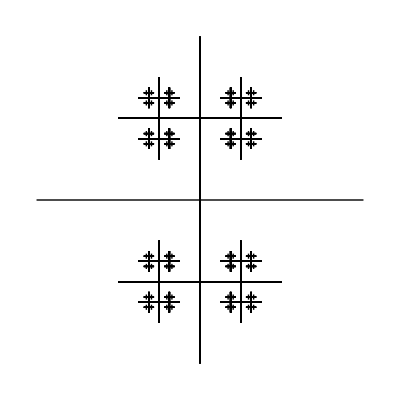

```mathematica
IDK[n_,p1_,p2_]:=If[n==0,
Return[{{p1,p2}}];,
Return[Join[
IDK[n-1,(p1+p2)/2,(p1+p2)/2+{{Cos[90°],-Sin[90°]},{Sin[90°],Cos[90°]}}.(p2-p1)/2],
IDK[n-1,(p1+p2)/2,(p1+p2)/2-{{Cos[90°],-Sin[90°]},{Sin[90°],Cos[90°]}}.(p2-p1)/2],
IDK[n-1,p1,p2]
]
]
]

Graphics[Line[IDK[7,{0,0},{1,0}]]]
```

```mathematica
SquareKoch[n_,p1_,p2_]:=If[n==0,
Return[{{p1,p2}}],
Return[Join[
SquareKoch[n-1,p1,p1+(p2-p1)/3],
SquareKoch[n-1,p1+(p2-p1)/3,p1+(p2-p1)/3+{{Cos[90°],-Sin[90°]},{Sin[90°],Cos[90°]}}.(p2-p1)/3],
SquareKoch[n-1,p1+(p2-p1)/3+{{Cos[90°],-Sin[90°]},{Sin[90°],Cos[90°]}}.(p2-p1)/3,p1+2*(p2-p1)/3+{{Cos[90°],-Sin[90°]},{Sin[90°],Cos[90°]}}.(p2-p1)/3],
SquareKoch[n-1,p2-(p2-p1)/3+{{Cos[90°],-Sin[90°]},{Sin[90°],Cos[90°]}}.(p2-p1)/3,p2-(p2-p1)/3],
SquareKoch[n-1,p2-(p2-p1)/3,p2]
]
]
]

SquareSnowflake[n_]:=Graphics[Line[Join[SquareKoch[n,{0,0},{0,1}],SquareKoch[n,{0,1},{1,1}],SquareKoch[n,{1,1},{1,0}],SquareKoch[n,{1,0},{0,0}]]]]

SquareSnowflake[6]
```

-Graphics-

```mathematica
Spiral[n_,r_,p1_,p2_]:=If[n==0,
Return[{{p1,p2}}],
Return[Join[
{{p1,p2}},
Spiral[n-1,p2,p2+r*{{Cos[-90°],-Sin[-90°]},{Sin[-90°],Cos[-90°]}}.(p2-p1)]
]
]
]

GoldenSpiral[n_]:=Graphics[Line[Spiral[n,1/GoldenRatio,{0,0},{1,0}]]]

GoldenSpiral[0];
```

```mathematica
Kochs[n_]:=Module[{i,CurrentIteration=List[{0,0},{1,0}],Copy1,Copy2,Copy3,Copy4},
For[i=1,i<=n,i++,
Copy1=Map[#/3&,CurrentIteration,{-1}];
Copy2=Map[{{Cos[60°],-Sin[60°]},{Sin[60°],Cos[60°]}}.#+Copy1[[2]]&,Copy1,{-1}];
Copy3=Map[{{Cos[-60°],-Sin[-60°]},{Sin[-60°],Cos[-60°]}}.(#-Copy1[[2]])+2*Copy1[[2]]&,Copy1,{-1}];
Copy4=Map[#+2*Copy1[[2]]&,Copy1,{-1}];
CurrentIteration={Copy1,Copy2,Copy3,Copy4};
];
Return[CurrentIteration];
]
Kochs[1]
```

{{{0,0},{1/3,0}},{{{1/3+{{1/2,-(√3)/2},{(√3)/2,1/2}}.0,{{1/2,-(√3)/2},{(√3)/2,1/2}}.0},{1/3+{{1/2,-(√3)/2},{(√3)/2,1/2}}.0,{{1/2,-(√3)/2},{(√3)/2,1/2}}.0}},{{1/3+{{1/2,-(√3)/2},{(√3)/2,1/2}}.1/3,{{1/2,-(√3)/2},{(√3)/2,1/2}}.1/3},{1/3+{{1/2,-(√3)/2},{(√3)/2,1/2}}.0,{{1/2,-(√3)/2},{(√3)/2,1/2}}.0}}},{{{1/2,1/(2 √3)},{1/2,1/(2 √3)}},{{2/3+1/(2 √3),1/6},{1/2,1/(2 √3)}}},{{{2/3,0},{2/3,0}},{{1,1/3},{2/3,0}}}}